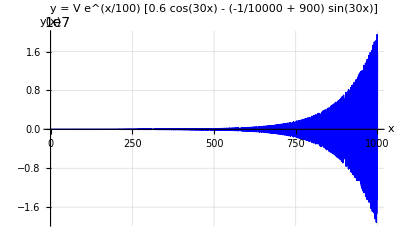

```mathematica
V=1; (*You can change this to your desired amplitude*)
y[x_]:=V*Exp[x/100]*(0.6*Cos[30*x]-(-1/10000+900)*Sin[30*x])

Plot[y[x],{x,0,1000},PlotRange->All,PlotStyle->{Thick,Blue},AxesLabel->{"x","y(x)"},GridLines->Automatic,PlotLabel->"y = V e^(x/100) [0.6 cos(30x) - (-1/10000 + 900) sin(30x)]"]
```